Here’s the windowing stuff so far:

### Import:

```mathematica
data$raw=Import["P:\\+Research\\GitWood\\stackCommits\\glance-openstack-commits.json","Data"]
```

{{author→Null,6,commit→{message→Merge "Add note to docs on release notes prelude section",4,tree→{url→https://api.github.com/repos/openstack/glance/git/trees/cb6a3954ac1174efac60cb2b0391f7ba872592db,sha→cb6a3954ac1174efac60cb2b0391f7ba872592db}}},{1},5568,{1},{author→Null,6,commit→{1}}}
 |  |  |  |

### Example Data:

```mathematica
data$raw[[1]]
```

{author→Null,url→https://api.github.com/repos/openstack/glance/commits/d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,committer→{events_url→https://api.github.com/users/openstack-gerrit/events{/privacy},following_url→https://api.github.com/users/openstack-gerrit/following{/other_user},avatar_url→https://avatars.githubusercontent.com/u/903479?v=3,site_admin→False,login→openstack-gerrit,gravatar_id→,url→https://api.github.com/users/openstack-gerrit,organizations_url→https://api.github.com/users/openstack-gerrit/orgs,gists_url→https://api.github.com/users/openstack-gerrit/gists{/gist_id},received_events_url→https://api.github.com/users/openstack-gerrit/received_events,html_url→https://github.com/openstack-gerrit,repos_url→https://api.github.com/users/openstack-gerrit/repos,subscriptions_url→https://api.github.com/users/openstack-gerrit/subscriptions,starred_url→https://api.github.com/users/openstack-gerrit/starred{/owner}{/repo},type→User,id→903479,followers_url→https://api.github.com/users/openstack-gerrit/followers},html_url→https://github.com/openstack/glance/commit/d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,sha→d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,comments_url→https://api.github.com/repos/openstack/glance/commits/d8461e5528c78e0c8c49a8e51c4f51a182c58ecd/comments,parents→{{url→https://api.github.com/repos/openstack/glance/commits/b9237e33f7aa61c0f880e482b1c55301723c7efc,html_url→https://github.com/openstack/glance/commit/b9237e33f7aa61c0f880e482b1c55301723c7efc,sha→b9237e33f7aa61c0f880e482b1c55301723c7efc},{url→https://api.github.com/repos/openstack/glance/commits/a75ddd4112f2d7297ffa5aad45b450246dadcae5,html_url→https://github.com/openstack/glance/commit/a75ddd4112f2d7297ffa5aad45b450246dadcae5,sha→a75ddd4112f2d7297ffa5aad45b450246dadcae5}},commit→{message→Merge "Add note to docs on release notes prelude section",author→{email→jenkins@review.openstack.org,date→2016-09-23T17:06:03Z,name→Jenkins},url→https://api.github.com/repos/openstack/glance/git/commits/d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,committer→{email→review@openstack.org,date→2016-09-23T17:06:03Z,name→Gerrit Code Review},comment_count→0,tree→{url→https://api.github.com/repos/openstack/glance/git/trees/cb6a3954ac1174efac60cb2b0391f7ba872592db,sha→cb6a3954ac1174efac60cb2b0391f7ba872592db}}}

### Rule Replacement:

```mathematica
r1=data$raw[[1]][[5]]
```

sha→d8461e5528c78e0c8c49a8e51c4f51a182c58ecd

```mathematica
"sha"->"d8461e5528c78e0c8c49a8e51c4f51a182c58ecd"
```

sha→d8461e5528c78e0c8c49a8e51c4f51a182c58ecd

```mathematica
Replace["sha",r1]
```

d8461e5528c78e0c8c49a8e51c4f51a182c58ecd

### Dates:

```mathematica
date$test="date"/.("author"/.({"commit"}/.data$raw[[1]])[[1]][[2]])[[2]]
```

2016-09-23T17:06:03Z

```mathematica
DateObject[date$test]
```

Fri 23 Sep 2016 17:06:03GMT-4.

```mathematica
{"date"/.("author"/.({"commit"}/.#)[[1]][[2]])[[2]],"sha"/.#[[5]]}&/@data$raw[[#]]
```

Part::pkspec1: The expression #1 cannot be used as a part specification.

Part::partw: Part 2 of {{message→Merge "Add note to docs on release notes prelude section",author→{email→jenkins@review.openstack.org,date→2016-09-23T17:06:03Z,name→Jenkins},url→https://api.github.com/repos/openstack/glance/git/commits/d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,committer→{email→review@openstack.org,date→2016-09-23T17:06:03Z,name→Gerrit Code Review},comment_count→0,tree→{url→https://api.github.com/repos/openstack/glance/git/trees/cb6a3954ac1174efac60cb2b0391f7ba872592db,sha→cb6a3954ac1174efac60cb2b0391f7ba872592db}}} does not exist.

ReplaceAll::reps: {{{message→Merge "Add note to docs on release notes prelude section",author→{email→jenkins@review.openstack.org,date→2016-09-23T17:06:03Z,name→Jenkins},url→https://api.github.com/repos/openstack/glance/git/commits/d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,committer→{email→review@openstack.org,date→2016-09-23T17:06:03Z,name→Gerrit Code Review},comment_count→0,tree→{url→https://api.github.com/repos/openstack/glance/git/trees/cb6a3954ac1174efac60cb2b0391f7ba872592db,sha→cb6a3954ac1174efac60cb2b0391f7ba872592db}}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{message→Merge "Add note to docs on release notes prelude section",author→{email→jenkins@review.openstack.org,date→2016-09-23T17:06:03Z,name→Jenkins},url→https://api.github.com/repos/openstack/glance/git/commits/d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,committer→{email→review@openstack.org,date→2016-09-23T17:06:03Z,name→Gerrit Code Review},comment_count→0,tree→{url→https://api.github.com/repos/openstack/glance/git/trees/cb6a3954ac1174efac60cb2b0391f7ba872592db,sha→cb6a3954ac1174efac60cb2b0391f7ba872592db}}} does not exist.

ReplaceAll::reps: {{{message→Merge "Add note to docs on release notes prelude section",author→{email→jenkins@review.openstack.org,date→2016-09-23T17:06:03Z,name→Jenkins},url→https://api.github.com/repos/openstack/glance/git/commits/d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,committer→{email→review@openstack.org,date→2016-09-23T17:06:03Z,name→Gerrit Code Review},comment_count→0,tree→{url→https://api.github.com/repos/openstack/glance/git/trees/cb6a3954ac1174efac60cb2b0391f7ba872592db,sha→cb6a3954ac1174efac60cb2b0391f7ba872592db}}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of {commit} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {date/.{commit}⟦2⟧,sha/.#1⟦5⟧} cannot be used as a part specification.

{date/.{{message→Merge "Add note to docs on release notes prelude section",author→{email→jenkins@review.openstack.org,date→2016-09-23T17:06:03Z,name→Jenkins},url→https://api.github.com/repos/openstack/glance/git/commits/d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,committer→{email→review@openstack.org,date→2016-09-23T17:06:03Z,name→Gerrit Code Review},comment_count→0,tree→{url→https://api.github.com/repos/openstack/glance/git/trees/cb6a3954ac1174efac60cb2b0391f7ba872592db,sha→cb6a3954ac1174efac60cb2b0391f7ba872592db}}}⟦2⟧,1bbddb7ae3c5258c1b8b300dd0d8d06d48d2b7ee}⟦{date/.{commit}⟦2⟧,sha/.#1⟦5⟧}⟧

## Filter Func:

Generates a list of commit objects with the structure {time, sha, email, name}

```mathematica
filter[n_]:={DateObject["date"/.("author"/.({"commit"}/.data$raw[[n]])[[1]][[2]])[[2]]],"sha"/.data$raw[[n]][[5]],"email"/.("author"/.({"commit"}/.data$raw[[n]])[[1]][[2]])[[1]],"name"/.("author"/.({"commit"}/.data$raw[[n]])[[1]][[2]])[[3]]}
```

```mathematica
Length@data$raw
```

5572

```mathematica
list=filter[#]&/@Range[5572]
```

{{Fri 23 Sep 2016 17:06:03GMT-4.,d8461e5528c78e0c8c49a8e51c4f51a182c58ecd,jenkins@review.openstack.org,Jenkins},5570,{Fri 6 Aug 2010 03:06:42GMT-4.,78b45ee909994eef9fbdeba59bb91d9fc955272b,rick@quasar.racklabs.com,Rick Harris}}
 |  |  |  |

Now filtering out anything commited by jenkins:

```mathematica
list$filtered=Select[list,#[[4]]≠"Jenkins"&]
```

{{Thu 22 Sep 2016 20:12:42GMT-4.,b9237e33f7aa61c0f880e482b1c55301723c7efc,openstack-infra@lists.openstack.org,OpenStack Proposal Bot},3585,{Fri 6 Aug 2010 03:06:42GMT-4.,78b45ee909994eef9fbdeba59bb91d9fc955272b,rick@quasar.racklabs.com,Rick Harris}}
 |  |  |  |

```mathematica
Transpose[list$filtered][[1]]
```

{Thu 22 Sep 2016 20:12:42GMT-4.,Thu 22 Sep 2016 07:15:32GMT-4.,Fri 26 Aug 2016 07:10:29GMT-4.,Fri 16 Sep 2016 17:32:44GMT-4.,Fri 16 Sep 2016 07:54:09GMT-4.,3578,Tue 24 Aug 2010 04:32:57GMT-4.,Thu 12 Aug 2010 01:17:56GMT-4.,Wed 11 Aug 2010 22:54:34GMT-4.,Fri 6 Aug 2010 03:06:42GMT-4.}
 |  |  |  |

```mathematica
({"author"}/.data$raw[[1]])
```

{Null}

```mathematica
("author"/.({"commit"}/.data$raw[[1]])[[1]][[2]])[[3]]
```

name→Jenkins

```mathematica
Position[Transpose[list][[2]],"a75ddd4112f2d7297ffa5aad45b450246dadcae5"]
```

{{22}}

```mathematica
list[[22]]
```

{Fri 2 Sep 2016 16:39:07GMT-4.,a75ddd4112f2d7297ffa5aad45b450246dadcae5,nik.komawar@gmail.com,Nikhil Komawar}

### Windowing Test:

```mathematica
window$test=Select[list$filtered,DateObject[{2016,1}]<#[[1]]<DateObject[{2016,2}]&]
```

{{Fri 8 Jan 2016 16:01:18GMT-4.,38158e554560621fa85d36aa2c288c04a94fb527,stuart.mclaren@hp.com,Stuart McLaren},{Sat 9 Jan 2016 16:05:09GMT-4.,0d97af65b49a60465a4fe0114c26789922d2b439,ting.wang@easystack.cn,ting.wang},{Fri 29 Jan 2016 10:22:48GMT-4.,c686033348e7e90f9ef841552817bf9f07313310,dshakhray@mirantis.com,Darja Shakhray},{Fri 8 Jan 2016 09:37:01GMT-4.,8a38f9ad5d22329af5ae3a6c21de4521f8fc8e1f,lin.a.yang@intel.com,Lin Yang},{Wed 6 Jan 2016 23:31:10GMT-4.,3ec69b5bd44e74c2b7c64a04fa973d66c4abac25,brianna.poulos@jhuapl.edu,Brianna Poulos},{Tue 19 Jan 2016 06:37:48GMT-4.,0d89611c1e80fad1757bd92db377c39841610b4a,wangxiyuan@huawei.com,wangxiyuan},{Wed 13 Jan 2016 12:03:23GMT-4.,61ffb49f9e72ee53bee1fbc53fc54ca54d10eb3a,niall.bunting@hpe.com,Niall Bunting},{Fri 29 Jan 2016 15:53:30GMT-4.,5062e1bb50b1bbae5f56e2f82f96e6484c12e824,kkushaev@mirantis.com,kairat_kushaev},{Fri 15 Jan 2016 06:52:14GMT-4.,4fc9d7df5e1dc1f4d430871857317fa7cced7e68,leidong@unitedstack.com,zwei},{Tue 19 Jan 2016 13:37:05GMT-4.,6179e1e98808548f1c12a2b66784cac3c1e5ac0f,jokke@usr.fi,Erno Kuvaja},{Mon 25 Jan 2016 21:01:09GMT-4.,33ae05ee8687af39b3bddc5b448ace2a412dbf68,travis.tripp@hpe.com,Travis Tripp},{Thu 28 Jan 2016 22:01:55GMT-4.,1ebbfd3dc1694dc4f26e763da9eee833bb5d2545,smurugesan@vmware.com,Sabari Kumar Murugesan},{Fri 8 Jan 2016 21:08:49GMT-4.,8f0d6ea9c535f6ab09fc9b2ae84cf0bef2401ee4,flaper87@gmail.com,Flavio Percoco},{Mon 25 Jan 2016 21:17:52GMT-4.,6a16e10afc19ba24e9a1b298676933bd4e83d8a6,harlowja@yahoo-inc.com,Joshua Harlow},{Tue 26 Jan 2016 23:22:58GMT-4.,fbe7a4f42a913eda58df1dc1ee3b6ed4dc17d150,openstack-infra@lists.openstack.org,OpenStack Proposal Bot},{Tue 26 Jan 2016 17:13:26GMT-4.,19aed25f5b837732a7b7152f5332f8f7a71d95e9,kstepniewski@vmware.com,Karol Stepniewski},{Fri 22 Jan 2016 20:13:35GMT-4.,eab1567d48a18fa968c7b66c3641dd037da1f84e,brianna.poulos@jhuapl.edu,Brianna Poulos},{Tue 19 Jan 2016 11:11:50GMT-4.,e1b5d6d0b9740d2097e54b0af1cbb82fb5d58832,abhishek.kekane@nttdata.com,abhishekkekane},{Mon 25 Jan 2016 20:29:14GMT-4.,8b6b94363574432a87ad390b0c35704055e9066f,harlowja@yahoo-inc.com,Joshua Harlow},{Sun 24 Jan 2016 20:48:29GMT-4.,a2440202d3421d27b364b6f6cd0245ae19ab47db,openstack-infra@lists.openstack.org,OpenStack Proposal Bot},{Thu 21 Jan 2016 16:54:36GMT-4.,9526e05b96de510f548bb3c3a927a2e30f533b43,ronald.bradford@gmail.com,Ronald Bradford},{Thu 21 Jan 2016 20:40:03GMT-4.,0ab4869fe9952f05d646d6242246c751c22d70e6,harlowja@yahoo-inc.com,Joshua Harlow},{Fri 22 Jan 2016 11:28:22GMT-4.,005526111dc2cfb90c53ea1577b2d847e19b1a40,bo.wang@easystack.cn,Bo Wang},{Fri 22 Jan 2016 04:03:25GMT-4.,561668db17fc462c3ef7c17b47eaa72c74d9dec3,openstack-infra@lists.openstack.org,OpenStack Proposal Bot},{Fri 22 Jan 2016 00:29:21GMT-4.,28becd1aadd3b6f3ed1c656f79470a2a988e2c72,travis.tripp@hpe.com,Travis Tripp},{Thu 21 Jan 2016 20:47:26GMT-4.,948e467021d5f455526dadb1d028d388371ed924,harlowja@yahoo-inc.com,Joshua Harlow},{Wed 20 Jan 2016 03:26:09GMT-4.,eb2e7c04fec2d4650add1b7fb4a9df970ffea962,bo.wang@easystack.cn,Bo Wang},{Wed 20 Jan 2016 03:49:49GMT-4.,5ef5b351c0e2479c61107642339e63f30df532a3,bo.wang@easystack.cn,Bo Wang},{Fri 15 Jan 2016 22:12:35GMT-4.,44629deb81d153b673d520af44d384b59bfb1a31,mitsuhiro.tanino@hds.com,Mitsuhiro Tanino},{Mon 18 Jan 2016 12:12:54GMT-4.,5814440bb900a13c8ceea7e2c1f3d3e1e98b31f6,kkushaev@mirantis.com,kairat_kushaev},{Mon 18 Jan 2016 11:58:00GMT-4.,c59b164c41f650ceaefbd9220e590e05fa0d81ef,niall.bunting@hpe.com,Niall Bunting},{Mon 18 Jan 2016 06:25:08GMT-4.,37440954d30368ae2a0fcbd45802d7075a45853e,openstack-infra@lists.openstack.org,OpenStack Proposal Bot},{Sat 16 Jan 2016 16:43:55GMT-4.,ded6a40153364bb0c67deefadf479b15ed669e41,aj@suse.com,Andreas Jaeger},{Thu 14 Jan 2016 17:20:33GMT-4.,3680735b96201e5051cfff4a66a842ce4823d6cf,bo.wang@easystack.cn,Bo Wang},{Thu 14 Jan 2016 06:55:46GMT-4.,000c7ff540602e37d714f6bfea993221babc19dc,openstack-infra@lists.openstack.org,OpenStack Proposal Bot},{Wed 13 Jan 2016 00:54:29GMT-4.,ca5cdb59e136a54862f8132bc5b3f9867ae44390,boris@pavlovic.me,Boris Pavlovic},{Thu 7 Jan 2016 16:07:08GMT-4.,3ab790a720b3ec1e894f09f0fdcdde7943f8728e,niall.bunting@hpe.com,Niall Bunting},{Thu 7 Jan 2016 17:12:47GMT-4.,ec172a10fef5f9b12bcdfa01e50d62f204cd71cc,openstack-infra@lists.openstack.org,OpenStack Proposal Bot},{Wed 6 Jan 2016 22:16:33GMT-4.,2752fd6e161944f5875e4f4d0b4cdf4e178d05cd,brianna.poulos@jhuapl.edu,Brianna Poulos},{Mon 4 Jan 2016 04:14:00GMT-4.,515203eac7661a8823ba70a1e832f4a32d45b1d7,openstack-infra@lists.openstack.org,OpenStack Proposal Bot}}

### And Tallied:

```mathematica
Tally[Transpose[window$test][[4]]]
```

{{Stuart McLaren,1},{ting.wang,1},{Darja Shakhray,1},{Lin Yang,1},{Brianna Poulos,3},{wangxiyuan,1},{Niall Bunting,3},{kairat_kushaev,2},{zwei,1},{Erno Kuvaja,1},{Travis Tripp,2},{Sabari Kumar Murugesan,1},{Flavio Percoco,1},{Joshua Harlow,4},{OpenStack Proposal Bot,7},{Karol Stepniewski,1},{abhishekkekane,1},{Ronald Bradford,1},{Bo Wang,4},{Mitsuhiro Tanino,1},{Andreas Jaeger,1},{Boris Pavlovic,1}}

## Func:

```mathematica
windows[list_,start_,end_,space_]:=Module[{dates,datePairs,results},
dates=DateRange[start,end,space];
datePairs=Partition[dates,2,1];
results=Select[list$filtered,DateObject[{2016,1}]<#[[1]]<DateObject[{2016,2}]&];
Tally[Transpose[results][[4]]]
]
```

```mathematica
Partition[DateRange[DateObject[{2016,1}],DateObject[{2016,12}],Quantity[1,"month"]],2,1]
```

{{Fri 1 Jan 2016,Mon 1 Feb 2016},{Mon 1 Feb 2016,Tue 1 Mar 2016},{Tue 1 Mar 2016,Fri 1 Apr 2016},{Fri 1 Apr 2016,Sun 1 May 2016},{Sun 1 May 2016,Wed 1 Jun 2016},{Wed 1 Jun 2016,Fri 1 Jul 2016},{Fri 1 Jul 2016,Mon 1 Aug 2016},{Mon 1 Aug 2016,Thu 1 Sep 2016},{Thu 1 Sep 2016,Sat 1 Oct 2016},{Sat 1 Oct 2016,Tue 1 Nov 2016},{Tue 1 Nov 2016,Thu 1 Dec 2016}}

```mathematica
MapThread
```

```mathematica
windows[list$filtered,DateObject[{2016,1}],DateObject[{2016,2}],Quantity[1,"month"]]
```

{{Stuart McLaren,1},{ting.wang,1},{Darja Shakhray,1},{Lin Yang,1},{Brianna Poulos,3},{wangxiyuan,1},{Niall Bunting,3},{kairat_kushaev,2},{zwei,1},{Erno Kuvaja,1},{Travis Tripp,2},{Sabari Kumar Murugesan,1},{Flavio Percoco,1},{Joshua Harlow,4},{OpenStack Proposal Bot,7},{Karol Stepniewski,1},{abhishekkekane,1},{Ronald Bradford,1},{Bo Wang,4},{Mitsuhiro Tanino,1},{Andreas Jaeger,1},{Boris Pavlovic,1}}

```mathematica
window$test=Select[list$filtered,DateObject[{2016,1}]<#[[1]]<DateObject[{2016,2}]&]
```

Select::normal: Nonatomic expression expected at position 1 in Select[list$filtered,Jan 2016<#1⟦1⟧<Feb 2016&].

Select[list$filtered,Jan 2016<#1⟦1⟧<Feb 2016&]

```mathematica
dateSelect[list_,start_,increment_]:=Module[{},
Select[list,start<#[[1]]≤(start+increment)&]
]
dates=DateRange[DateObject[{2016,1}],DateObject[{2016,8}],Quantity[1,"month"]]
```

{Fri 1 Jan 2016,Mon 1 Feb 2016,Tue 1 Mar 2016,Fri 1 Apr 2016,Sun 1 May 2016,Wed 1 Jun 2016,Fri 1 Jul 2016,Mon 1 Aug 2016}

```mathematica
Map[dateSelect,{dates, DateObject[{2016,1}],Quantity[1,"month"]}]

mapTest[startDate_]:=Module[{},
Select[Range[10],startDate< #≤(startDate+1)&]
]
```

{dateSelect[{Fri 1 Jan 2016,Mon 1 Feb 2016,Tue 1 Mar 2016,Fri 1 Apr 2016,Sun 1 May 2016,Wed 1 Jun 2016,Fri 1 Jul 2016,Mon 1 Aug 2016}],dateSelect[Jan 2016],dateSelect[1 mo]}

```mathematica
Map[mapTest,Range[10]]
```

```mathematica
{{2},{3},{4},{5},{6},{7},{8},{9},{10},{}}
```

```mathematica
threadTest[list_,start_,increment_]:=Module[{},
Select[list,start<#≤(start+increment)&]
]
```

```mathematica
threadTest[Range[10],#,1]&/@Range[10]
```

{{2},{3},{4},{5},{6},{7},{8},{9},{10},{}}

## For loop :(

```mathematica
windowFor[list_,start_,end_,increment_]:=Module[{dates,results,windowResults},
Reap[
For[i=start,i<end,i=DatePlus[i,increment],
windowResults=Select[list,i<#[[1]]<DatePlus[i,increment*2]&];
Sow[Tally[Transpose[windowResults][[4]]]];
];
]
]
```

```mathematica
results=windowFor[list$filtered,DateObject[{2016,1}],DateObject[{2016,8}],Quantity[1,"month"]][[2]][[1]]
```

{{{Dinesh Bhor,2},{Dina Belova,1},{Erno Kuvaja,2},{Stuart McLaren,2},{Niall Bunting,5},{Abhishek Kekane,1},{Tomoki Sekiyama,1},{ting.wang,1},{Mike Fedosin,1},{Darja Shakhray,1},{Fei Long Wang,1},{Béla Vancsics,1},{Lin Yang,1},{Dane Fichter,2},{OpenStack Proposal Bot,15},{Andreas Jaeger,6},{ChangBo Guo(gcb),2},{Brianna Poulos,3},{Kent Wang,1},{Cyril Roelandt,5},{Qiaowei Ren,2},{Henrique Truta,1},{Victor Stinner,5},{wangxiyuan,2},{Davanum Srinivas,1},{Preetika,1},{Kirill Zaitsev,3},{kairat_kushaev,3},{Javeme,1},{Doug Hellmann,1},{jinxingfang,1},{zwei,1},{Justin Shepherd,1},{Travis Tripp,2},{Sabari Kumar Murugesan,1},{Flavio Percoco,1},{Joshua Harlow,4},{Karol Stepniewski,1},{abhishekkekane,1},{Ronald Bradford,1},{Bo Wang,4},{Mitsuhiro Tanino,1},{Boris Pavlovic,1}},{{Dinesh Bhor,2},{Dina Belova,1},{Flavio Percoco,1},{Erno Kuvaja,2},{bhagyashris,1},{Mike Turvey,1},{Fei Long Wang,2},{bria4010,2},{OpenStack Proposal Bot,21},{Nguyen Hung Phuong,1},{dineshbhor,1},{Niall Bunting,4},{Stuart McLaren,2},{Brandon Palm,1},{Thierry Carrez,2},{Mike Fedosin,2},{Tom Cocozzello,3},{Danny Al-Gaaf,2},{Cao ShuFeng,1},{Doug Hellmann,2},{Abhishek Kekane,1},{Sabari Kumar Murugesan,1},{Daniel Krook,1},{Tomoki Sekiyama,2},{David Sariel,1},{Michael Krotscheck,1},{Béla Vancsics,1},{Dane Fichter,2},{Andreas Jaeger,5},{ChangBo Guo(gcb),2},{Kent Wang,1},{Cyril Roelandt,5},{Qiaowei Ren,2},{Henrique Truta,1},{Victor Stinner,5},{wangxiyuan,1},{Davanum Srinivas,1},{Preetika,1},{Kirill Zaitsev,3},{Javeme,1},{jinxingfang,1},{Justin Shepherd,1},{kairat_kushaev,1}},{{bria4010,3},{Flavio Percoco,1},{ZhiQiang Fan,1},{OpenStack Proposal Bot,23},{Niall Bunting,3},{Hemanth Makkapati,2},{Dane Fichter,1},{bhagyashris,1},{Sachin Patil,1},{Gregory Haynes,1},{Mike Turvey,1},{Pankaj Mishra,2},{Thomas Bechtold,1},{Fei Long Wang,1},{Jamie Lennox,1},{DeepaJon,1},{Danny Al-Gaaf,3},{bpankaj,1},{Juan Antonio Osorio Robles,1},{venkatamahesh,1},{kairat_kushaev,1},{Tom Cocozzello,4},{Nguyen Hung Phuong,1},{dineshbhor,1},{Stuart McLaren,1},{Brandon Palm,1},{Thierry Carrez,2},{Mike Fedosin,1},{Cao ShuFeng,1},{Doug Hellmann,1},{Erno Kuvaja,1},{Sabari Kumar Murugesan,1},{Daniel Krook,1},{Tomoki Sekiyama,1},{David Sariel,1},{Michael Krotscheck,1}},{{Flavio Percoco,1},{Hemanth Makkapati,5},{Nikhil Komawar,3},{Jamie Lennox,2},{bria4010,2},{Nolwenn Cauchois,1},{Castulo J. Martinez,1},{Brianna Poulos,1},{OpenStack Proposal Bot,17},{Alfredo Moralejo,1},{kairat_kushaev,2},{WenjunWang1992,1},{Alexander Tivelkov,1},{Bertrand Lallau,1},{liangjingtao,1},{Stuart McLaren,1},{zhufl,1},{ZhiQiang Fan,1},{Niall Bunting,1},{Dane Fichter,1},{Sachin Patil,1},{Gregory Haynes,1},{Pankaj Mishra,2},{Thomas Bechtold,1},{DeepaJon,1},{Danny Al-Gaaf,1},{bpankaj,1},{Juan Antonio Osorio Robles,1},{venkatamahesh,1},{Tom Cocozzello,1}},{{Mike Fedosin,2},{Flavio Percoco,1},{Hemanth Makkapati,3},{Nikhil Komawar,5},{bria4010,5},{Dharini Chandrasekar,2},{Jamie Lennox,2},{bhagyashris,1},{OpenStack Proposal Bot,14},{Brianna Poulos,2},{Niall Bunting,4},{zhengyao1,1},{Nolwenn Cauchois,1},{Sabari Kumar Murugesan,2},{Castulo J. Martinez,1},{Gary Kotton,1},{Eric Brown,1},{Alfredo Moralejo,1},{kairat_kushaev,1},{WenjunWang1992,1},{Alexander Tivelkov,1},{Bertrand Lallau,1},{liangjingtao,1},{Stuart McLaren,1},{zhufl,1}},{{Mike Fedosin,2},{Dharini Chandrasekar,10},{Itisha Dewan,1},{Nikhil Komawar,5},{Hemanth Makkapati,2},{Marc Abramowitz,6},{OpenStack Proposal Bot,11},{Stuart McLaren,2},{ke-kuroki,1},{dineshbhor,1},{bria4010,6},{Alexander Bashmakov,1},{raiesmh08,1},{Erno Kuvaja,1},{yuyafei,2},{weiweigu,1},{Ronald Bradford,1},{“Akhila,1},{Bin Zhou,1},{Niall Bunting,5},{Fei Long Wang,1},{bhagyashris,1},{Brianna Poulos,1},{zhengyao1,1},{Sabari Kumar Murugesan,2},{Gary Kotton,1},{Jamie Lennox,1},{Eric Brown,1}},{{hussainchachuliya,1},{Nikhil Komawar,12},{Dharini Chandrasekar,11},{Alexander Bashmakov,5},{Hemanth Makkapati,5},{Dane Fichter,2},{OpenStack Proposal Bot,14},{Brian Rosmaita,2},{Itisha Dewan,1},{Luong Anh Tuan,1},{Darren White,1},{Cao Xuan Hoang,1},{Li Wei,1},{Stephen Gordon,1},{Atsushi SAKAI,1},{Graham Hayes,1},{Thomas Bechtold,1},{Stephen Finucane,1},{Sean Dague,1},{ChangBo Guo(gcb),1},{Niall Bunting,2},{Jin Li,1},{Travis Tripp,1},{Gábor Antal,1},{Chen Fan,1},{Marc Abramowitz,6},{Stuart McLaren,2},{ke-kuroki,1},{dineshbhor,1},{bria4010,2},{raiesmh08,1},{Erno Kuvaja,1},{yuyafei,2},{weiweigu,1},{Ronald Bradford,1},{“Akhila,1},{Bin Zhou,1},{Fei Long Wang,1}}}

```mathematica
list$filtered
```

list$filtered

```mathematica
Select[DateRange[DateObject[{2016,1}],DateObject[{2016,8}],Quantity[1,"Months"]],DateObject[{2016,2}]<#<DateObject[{2016,4}]&]
```

{Tue 1 Mar 2016}

```mathematica
results
```

{{Dinesh Bhor,2},{Dina Belova,1},{Erno Kuvaja,2},{Stuart McLaren,2},{Niall Bunting,5},{Abhishek Kekane,1},{Tomoki Sekiyama,1},{ting.wang,1},{Mike Fedosin,1},{Darja Shakhray,1},{Fei Long Wang,1},{Béla Vancsics,1},{Lin Yang,1},{Dane Fichter,2},{OpenStack Proposal Bot,15},{Andreas Jaeger,6},{ChangBo Guo(gcb),2},{Brianna Poulos,3},{Kent Wang,1},{Cyril Roelandt,5},{Qiaowei Ren,2},{Henrique Truta,1},{Victor Stinner,5},{wangxiyuan,2},{Davanum Srinivas,1},{Preetika,1},{Kirill Zaitsev,3},{kairat_kushaev,3},{Javeme,1},{Doug Hellmann,1},{jinxingfang,1},{zwei,1},{Justin Shepherd,1},{Travis Tripp,2},{Sabari Kumar Murugesan,1},{Flavio Percoco,1},{Joshua Harlow,4},{Karol Stepniewski,1},{abhishekkekane,1},{Ronald Bradford,1},{Bo Wang,4},{Mitsuhiro Tanino,1},{Boris Pavlovic,1}}

ReplaceAll::reps: {names} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

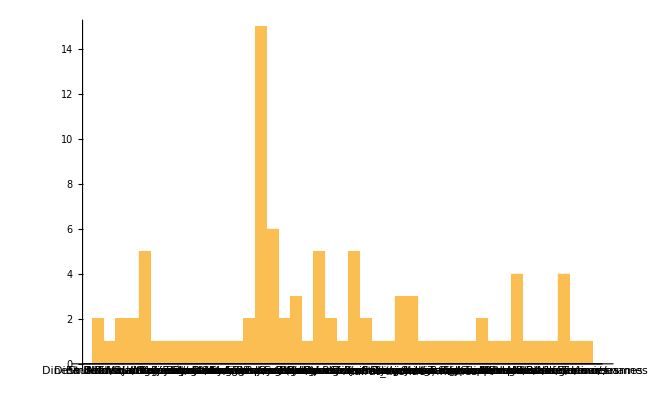

```mathematica
BarChart[Labeled[#2,#1/.names]&@@@results[[1]]]
```